```mathematica
vec[{i_,j_,k_},colour_]:=Graphics3D[{colour,Thick,Arrow[{{0,0,0},{i,j,k}}]}]
```

```mathematica
vecPlot[vecs_]:=Show[vec[vecs[[1]],Red],vec[vecs[[2]],Green],vec[vecs[[3]],Blue],Axes->True,AxesOrigin->{0,0,0},Boxed->False,AxesLabel->{"X","Y","Z"},ImageSize->Large,PlotRange->Max[Norm/@vecs]{{-1,1},{-1,1},{-1,1}}]
```

```mathematica
A={{1,2,3},{4,5,6},{7,8,9}};
```

```mathematica
vecPlot[Transpose[A]]
```

-Graphics3D-

```mathematica
A={{1,2,3},{4,5,6},{7,8,10}};
```

```mathematica
{a1,a2,a3}=Transpose[A];
```

```mathematica
vecPlot[{a1,a2,a3}]
```

-Graphics3D-

```mathematica
vec[a1,Red]
```

-Graphics3D-

```mathematica
Show[vec[A[[All,1]],Red],vec[A[[All,2]],Green],vec[A[[All,3]],Blue],Axes->True,AxesOrigin->{0,0,0},Boxed->False,AxesLabel->{"X","Y","Z"},ImageSize->Large,PlotRange->10{{-1,1},{-1,1},{-1,1}}]
```

-Graphics3D-

```mathematica
4195835/3145727//N
```

1.33382

```mathematica
vec[1,2,2]
```

-Graphics3D-

```mathematica
Graphics3D[Arrow[{1,1,1}],Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->Large]
```

-Graphics3D-

```mathematica
?Epilog
```

```mathematica
RotationMatrix[π/2].{-1/2,2}
```

{-2,-1/2}

```mathematica
Graphics[Text[Style["Mirror",16,Italic,FontFamily->"Times"],{2,1/10}]]
```

-Graphics-

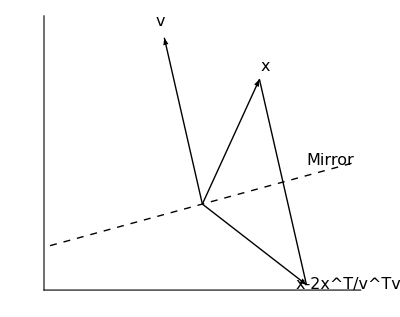

```mathematica
Show[Graphics[Arrow[{{0,0},{3/4,3/2}}]],Graphics[Arrow[{{0,0},{-1/2,2}}]],Graphics[Arrow[{{0,0},{3/4,3/2}-2({3/4,3/2}.{-1/2,2})/({-1/2,2}.{-1/2,2}){-1/2,2}}]],Graphics[Line[{{3/4,3/2}-2({3/4,3/2}.{-1/2,2})/({-1/2,2}.{-1/2,2}){-1/2,2},{3/4,3/2}}]],Graphics[{Dashed,Line[{{-2,-1/2},{2,1/2}}]}],Graphics[Text[Style["x",16,Italic,FontFamily->"Times"],1.1{3/4,3/2}]],Graphics[Text[Style["v",16,Italic,FontFamily->"Times"],1.1{-1/2,2}]],Graphics[Text[Style["x-2x^T/v^Tv",16,Italic,FontFamily->"Times"],{1.4,1}({3/4,3/2}-2({3/4,3/2}.{-1/2,2})/({-1/2,2}.{-1/2,2}){-1/2,2})]],Graphics[Rotate[Text[Style["Mirror",16,Italic,FontFamily->"Times"],{7/4,1/10}],ArcTan[1/2/2],{0,0}]],Axes->True,Ticks->None,PlotRange->All(*{{-2,2},{-5/4,3}}*)]
```